```mathematica
ClearAll[E1,Sfunc,A,DsFunc,plotE1,tValues,p,t,newResults,generatePlotAndRoots];

(*Define the electric field function*)
E1[t_]:=Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2t];
A[tx_]=-Integrate[E1[t],t]/. t->tx;

(*Function to generate plots and roots for a given p*)
generatePlotAndRoots[p_]:=
Module[
{Ip=0.5,Sf,Sfunc,DsFunc,realMin,realMax,imagMin,imagMax,realSteps,imagSteps,listofseeds,allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues,plotE1,plotRoots},

(*Define Sf,Sfunc,and DsFunc*)
Sf[ty_]=Integrate[2 p*A[t]+(A[t])^2,t]/. t->ty;
Sfunc[t_]:=0.5*Sf[t]+(0.5*p^2+Ip)*t;
DsFunc[t_]:=D[Sfunc[tz],tz]/. tz->t;

(*Generate the grid of seeds*)realMin=-2.133;realMax=4.15;
imagMin=0;imagMax=3;
realSteps=10;imagSteps=5;
listofseeds=Flatten[
Table[
x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}
],1];

(*Find roots*)
allSolutions=Round[t/. Quiet[
Table[
FindRoot[DsFunc[t]==0,{t,tseed}],
{tseed,listofseeds}]
],0.0001];

complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];

(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#]]]<=tolerance&&Abs[Im[DsFunc[#]]]<=tolerance&];

(*Plot E1 and the roots*)
plotE1=Quiet[
Plot[
E1[t],
{t,realMin,realMax},

PlotLabel->"p = "<>ToString[p],
AxesLabel->{"Time, t","Electric Field"},
ImageSize-> Large]
];

plotRoots=Quiet[
ListPlot[
{{Re[#],E1[Re[#]]}&/@filteredTValues},

PlotStyle->{Red,PointSize[0.02]},
AxesLabel->{"Time, t","Electric Field"},
ImageSize-> Large
]
];

(*Return both the plot and filteredTValues*)
{Show[plotE1,plotRoots,PlotRange->All],filteredTValues}];

(*Electric field plot along with saddle points as red dots,and for the slider for p from-3 to 3.*)
Manipulate[
Module[
{plotData,plotE1,plotRoots,filteredTValues},
plotData=generatePlotAndRoots[p];
plotE1=plotData[[1]];
filteredTValues=plotData[[2]];

plotRoots=ListPlot[
{{Re[#],E1[Re[#]]}&/@filteredTValues},

PlotStyle->{Red,PointSize[0.02]},
AxesLabel->{"Time, t","Electric Field"},
ImageSize-> Large
];

Show[plotE1,plotRoots,PlotRange->All]
],
{{p,0,"Momentum p"},-3,3,0.1} 
]
```

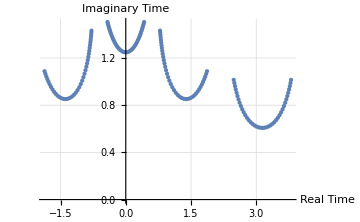

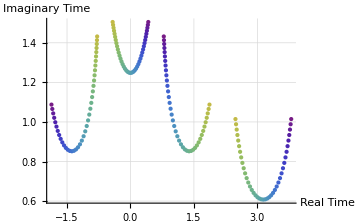

```mathematica
ClearAll[pValues,newResults,results,newTuple,tsExtended,validData,realAndImagTimes,colorFunction,coloredPoints];

pValues=Range[-2,2,0.1];

(*Generate results using the precise pValues*)
results=Table[
generatePlotAndRoots[p],{p,pValues}
];

newResults=Table[
{pValue=-3+(i-1)*0.1,results[[i,2]]},
{i,Length[results]}
];

tsExtended=Map[
Join[
{#[[1]]},PadRight[#[[2]],4,Null]
]&,newResults];

(*Filter and prepare the data for further processing*)
validData=Select[
Flatten[
Table[
If[
tsExtended[[i,j+1]]=!=Null,
{Re[tsExtended[[i,j+1]]],Im[tsExtended[[i,j+1]]],tsExtended[[i,1]]},
Nothing],
{i,Length[tsExtended]},
{j,1,4}]
,1],
#[[1]]=!=Null&];

(*Extract real and imaginary times*)
realAndImagTimes=validData[[All,1;;2]];

(*Plot the 2D graph*)
ListPlot[
realAndImagTimes,

AxesLabel->{"Real Time","Imaginary Time"},
PlotStyle->PointSize[Medium],
GridLines->Automatic,
ImageSize->Medium]


colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Generate a list of colored points with the custom color function*)
coloredPoints=Table[
{colorFunction[validData[[i,3]]]
,Point[validData[[i,1;;2]]]
},
{i,1,Length[validData]}
];

(*Plot the 2D graph with the custom color grading for momentum*)
Show[
Graphics[
{coloredPoints},

Axes->True,
AxesLabel->{"Real Time","Imaginary Time"},
GridLines->Automatic],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/GoldenRatio]
```

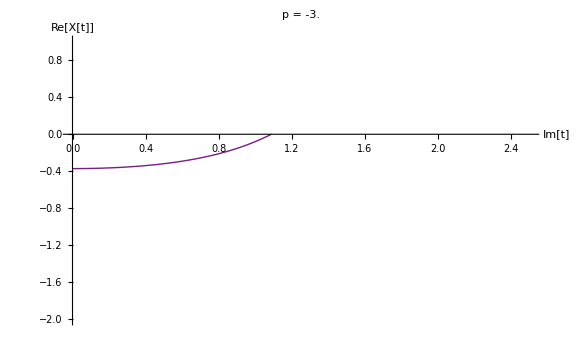
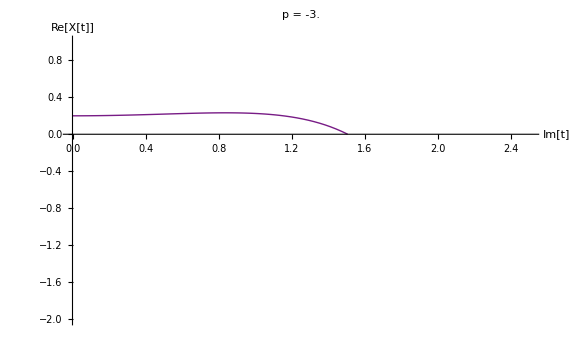
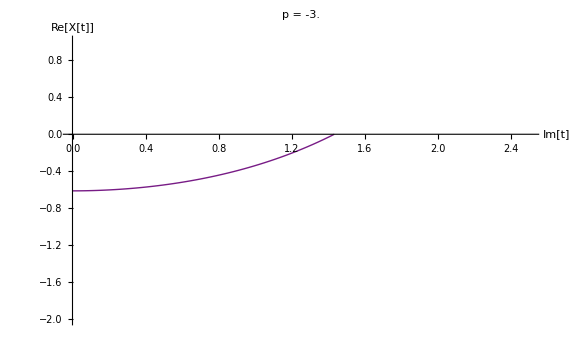
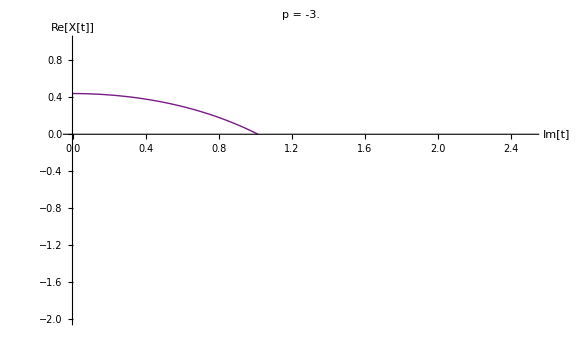
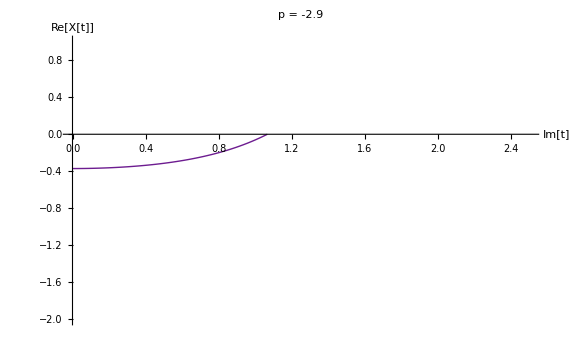
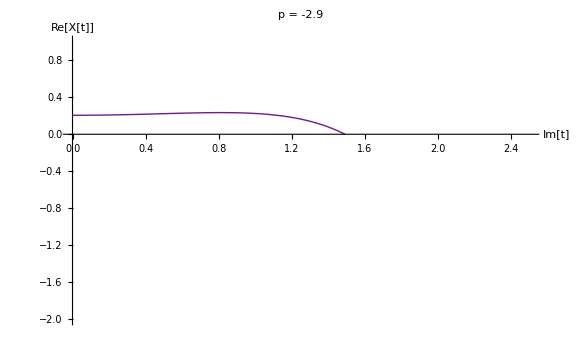
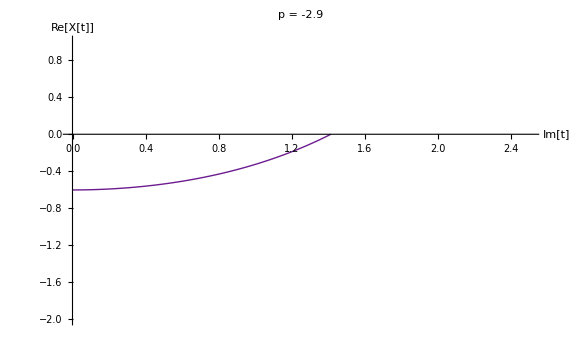
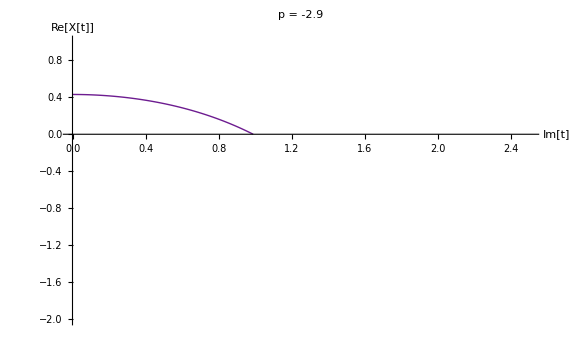
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ClearAll[X1, X, fixedPlotRange,imaginaryPlots, combinedImaginaryPlots];

X1[t_,p_]=Evaluate[Integrate[p+A[t],t]];
X[t_,p_,ts_]:=X1[t,p]-X1[ts,p];
(*Real trajectory vs Imaginary time*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Define a fixed plot range for comparison*)
fixedPlotRange={{0,2.5},{-2,1}}; 

(*Collect individual plots for each saddle point*)
imaginaryPlots=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[Re[X[Re[tsExtended[[k,i]]]+I ti,p,tsExtended[[k,i]]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->(*All*)fixedPlotRange,
AxesLabel->{"Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p],
ImageSize->Large]
],
{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedImaginaryPlots=
Table[
Show[
imaginaryPlots[[All,i]],

PlotRange->(*All*)fixedPlotRange,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedImaginaryPlots
```

```mathematica
ClearAll[threeDPlots,combinedThreeDPlots];
(*3D plot of the whole trajectory inside and outside the tunnel, ReX vs ReT vs ImT*)
(*Collect individual plots for each saddle point*)
threeDPlots=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Re[tr+I ti],Im[tr+I ti],Re[X[tr+I ti,p,tsExtended[[k,i]]]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Re[t]","Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]],

ParametricPlot3D[
{Re[tr+I ti],Im[tr+I ti],Re[X[tr+I ti,p,tsExtended[[k,i]]]]}
/. ti->0.,
{tr,Re[tsExtended[[k,i]]],Re[tsExtended[[k,i]]]+2 Pi},

PlotRange->All,
AxesLabel->{"Re[t]","Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}]
],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots=
Table[
Show[
threeDPlots[[All,i]],

PlotRange-> All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ClearAll[threeDPlots2,combinedThreeDPlots2];
(*3D plot of real and imaginary trajectories against imaginary time*)
(*Collect individual plots for each saddle point*)
threeDPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[X[tr+I ti,p,tsExtended[[k,i]]]],Re[X[tr+I ti,p,tsExtended[[k,i]]]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[X[t]]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots2=
Table[
Show[
threeDPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
xyz = Show[%,PlotRange-> All]
```

-Graphics3D-

```mathematica
ClearAll[V1,imaginaryPlots2, combinedImaginaryPlots2];
(*Imaginary Velocity vs Imaginary time*)
V1[t_,p_]:=p+A[t];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
imaginaryPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[Im[V1[Re[tsExtended[[k,i]]]+I ti,p]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[V[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p]]
],
{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedImaginaryPlots2=
Table[
Show[
imaginaryPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)

combinedImaginaryPlots2
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*3D plot of real and imaginary velocities against imaginary time*)

ClearAll[V1,threeDPlots2, combinedThreeDPlots2];

V1[t_,p_]:=p+A[t];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
threeDPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[V1[tr+I ti,p]],Re[V1[tr+I ti,p]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[V[t]]","Re[V[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots2=
Table[
Show[
threeDPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange-> All]
```

-Graphics3D-

```mathematica
(*Real Electric field for all saddle points (with different moment p) against imaginary time.*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
imaginaryPlots1=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[
Re[E1[Re[tsExtended[[k,i]]]+I ti]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Re[E1[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p]]
],
{k,1,Length[tsExtended]},{i,2,5}
];

(*Combine plots for each saddle point*)
combinedImaginaryPlots1=
Table[
Show[
imaginaryPlots1[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large
],
{i,1,4}
];

(*Display combined plots*)
combinedImaginaryPlots1
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*3D plot of real and imaginary electric field against imaginary time*)
ClearAll[threeDPlots3, combinedThreeDPlots3];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
threeDPlots3=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[E1[Re[tsExtended[[k,i]]]+I ti]],Re[E1[Re[tsExtended[[k,i]]]+I ti]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[E1[t]]","Re[E1[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots3=
Table[
Show[
threeDPlots3[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots3
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange->All]
```

-Graphics3D-